```mathematica
NotebookSave[]
(*Parameter for later calculation*)
g=9.81;
θ0=π/20;
ω=√((3 g (r-b))/(5 b^2));

(*Center of Mass of Cube, θ - Angle of Inclination, r - radius of cylinder, b - half length of cube's side*)
posCM[θ_,r_,b_]:={(r+b)Sin[θ]-r θ Cos[θ],(r+b)Cos[θ]+r θ Sin[θ]}; 
(*Function to draw square section of cube*)
drawSquare[θ_,r_,b_]:={EdgeForm[{Thick,Blue}],FaceForm[],Rotate[Rectangle[posCM[θ,r,b]-{b,b},posCM[θ,r,b]+{b,b}],-θ]}
(*Initial Values for θ, r, and b*)
θ=0;
r=2;
b=1;
(*Function to numerically find critical angle*)
tcrit[r_,b_]:=t/.FindRoot[Tan[t]-r/b t==0,{t,1.5}]
(*Diagram of problem, manipulating θ, r, and b*)
Manipulate[
{
Show[
Graphics[{
drawSquare[θ,r,b],(*Section of Cube*)
Circle[{0,0},r],(*Secton of cylinder*)
Line[{{0,0},{r,0}}],(*Line of Cylinder's Radius*)
Line[{{0,0},{(r+b)Sin[θ],(r+b)Cos[θ]}}],(*Line form center of cylinder to center of mass of cube*)
Line[{posCM[θ,r,b],{(r+b)Sin[θ],(r+b)Cos[θ]}}],(*Line from center of cube to extension of radius, passing through the tangent point between cylinder and cube*)
Dashed,
InfiniteLine[{{0,0},{0,1}}],(*Vertical y-axis*)
InfiniteLine[{posCM[θ,r,b],posCM[θ,r,b]+{1,0}}],(*horizontal line going through cube's center of mass*)
InfiniteLine[{{0,0},{Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}],(*Line indicating positive critical angle*)
InfiniteLine[{{0,0},{-Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}](*Line indicating negative critical angle*)
}]
,PlotRange->{{-1.1(r+2b),1.1(r+2b)},{-1.1r,1.1(r+2b)}},ImageSize->Large]
,
Show[
Plot[posCM[θ,r,b][[2]],{θ,-π,π},PlotRange->{0,6},AxesLabel->{"θ","Height of C_m"},Ticks->{Range[-π,π,π/4],Range[1,6,1]}],
Graphics[{
Dashed,
InfiniteLine[{{θ,0},{θ,1}}]
}]
,ImageSize->Large]
}//Row
,{{θ,0},-π,π},{{r,2},0,10},{{b,1},0,10}]
```

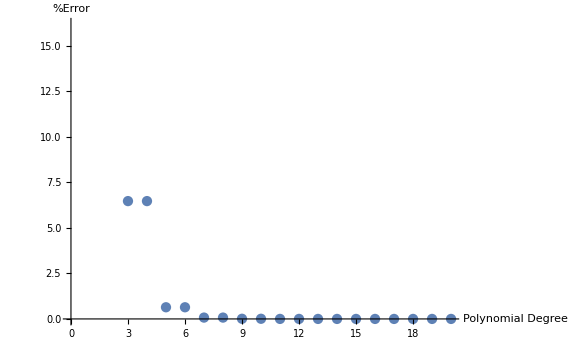

```mathematica
(*Exact value of critical angle for a given r and b*)
exactValue=t/.FindRoot[Tan[t]-r/b t==0,{t,1}];
(*List of approximate values for the calculation fo the critical angle depending on the degree of expansion of Tan[t] function*)
approxValue=t/.Table[FindRoot[Normal[Series[Tan[t],{t,0,n}]]-r/b t==0,{t,20}],{n,1,20}];
(*%Error of each approximation*)
percentErrors=Abs[approxValue-exactValue]/exactValue*100;
(*Plor of %Error of calculation of critical angle depending on the degree of approximation*)
ListPlot[percentErrors,AxesLabel->{"Polynomial Degree","%Error"},ImageSize->Large]
```

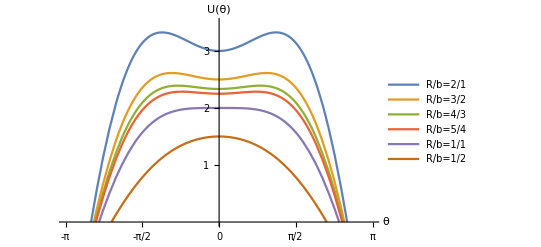

```mathematica
(*Plot of height of cube's center of mass depentend on the ration between r and b. to demosntrate inclection points of potential energy plot at different ratios*)
Plot[{posCM[θ,2,1][[2]],posCM[θ,3/2,1][[2]],posCM[θ,4/3,1][[2]],posCM[θ,5/4,1][[2]],posCM[θ,1,1][[2]],posCM[θ,.5,1][[2]]},{θ,-π,π},PlotRange->{0,3.5},AxesLabel->{Automatic,"U(θ)"},Ticks->{Range[-π,π,π/4],Range[1,6,1]},PlotLegends->LineLegend[{"R/b=2/1","R/b=3/2","R/b=4/3","R/b=5/4","R/b=1/1","R/b=1/2"}]]
```

```mathematica
(*Numerical solution for the angle of cube over time T[t] for given inital conditions and T'[t] == 0*)
sol=NDSolve[{T''[t](5/3 b^2+r^2 T[t]^2)+T'[t]^2 r^2 T[t]==g(b Sin[T[t]]-r T[t]Cos[T[t]]),T[0]==θ0,T'[0]==0},T[t],{t,0,30}]
```

{{T[t]→InterpolatingFunction[{{0., 30.}}, <>][t]}}

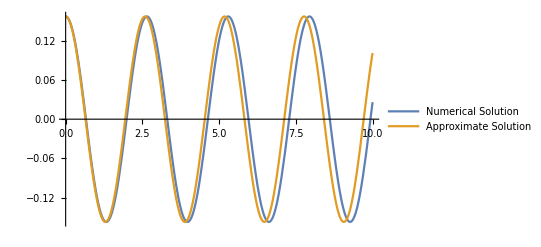

```mathematica
(*Plot comparing Numerical and Approximate Solutions for the angle of the cube over time*)
Plot[{T[t]/.sol,θ0 Cos[ω t]},{t,0,10},PlotLegends->LineLegend[{"Numerical Solution","Approximate Solution"}]]
```